```mathematica
ClearAll["Global'*"];
$PrePrint = MatrixForm;
```

```mathematica
(*Definicje stałych i funkcji*)
G=.01;
H=1;
rho0=1;
ymax=10;
v0[y_]:=(H y)
rho0y[y_]:=(
rho0 + 0.1 Sin[2Pi y / (2 ymax)](**)
)
m[y_]:=(Integrate[rho0y[yy],{yy,0,y}])
xi[y_,t_]:=(y+v0[y]t-2Pi G m[y]t^2)
a[t_]:=1+H t- 2 Pi G rho0 t^2   (*czynnik skali dla rho0y = const*)
xiDy[y_,t_]:=(1+H t-2Pi G rho0y[y] t^2) (*pochodna xi po y*)
xiDt[y_,t_]:=(v0[y]-4Pi G m[y]t) (*pochodna xi po t*)

rhokt[k_,t_]:=(
NIntegrate[rho0y[y] Exp[-I k xi[y,t]],{y,-ymax,ymax}]
)

vkt[k_,t_]:=(
NIntegrate[xiDt[y,t]Exp[-I k xi[y,t]]xiDy[y,t],{y,-ymax,ymax}]
)

rhokScaledt[k_,t_]:=(
NIntegrate[rho0y[y] Exp[-I k / a[t]   xi[y,t]],{y,-ymax,ymax}]
)

rhotxScaled[x_,t_]:=(
rho0y[(x/a[t])/a[t]]Abs[xiDy[(x/a[t])/a[t] ,t]]^(-1)
)

momentumDensityScaled[x_,t_]:=(
rho0y[(x/a[t])]Abs[xiDy[(x/a[t]) ,t]]^(-1) xiDt[(x/a[t]),t]
)
```

```mathematica
tmax=Max[t/.{Solve[xi[-ymax,t]==0,t][[2]],Solve[xi[ymax,t]==0,t][[2]]}]; (*Max z czasu zapadania obu końców*)
tbounce=Max[t/.{Solve[xiDt[-ymax,t]==0,t][[1]],Solve[xiDt[ymax,t]==0,t][[1]]}];
amax=FindMaximum[a[t],{t,tmax/2}][[1]];
Print["tmax: ",tmax, ", tbounce ",tbounce,", amax ",amax]
tstep=.05;
ts=Table[t,{t,0,tmax,tstep}];
k=10;
rhokScaled1=rhokScaledt[k,ts];
(*rhok1=rhokt[k,ts];
vk1=vkt[k,ts];*)
```

tmax: 16.8595, tbounce 7.95775, amax 4.97887

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-7.96875}. NIntegrate obtained 0.0125914-0.0160567 ⅈ and 2.37077×10^-8 for the integral and error estimates.

```mathematica
(*Wykresy pierwszego modu przeskalowanej transformaty gęstości*)
ListLinePlot[Thread[{ts,Re[rhokScaled1]}],PlotLabels->{"Re"}, PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red}},None},PlotRange->All]
ListLinePlot[Thread[{ts,Im[rhokScaled1]}],PlotLabels->{"Im"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red}},None},PlotRange->All]
ListLinePlot[Thread[{ts,Abs[rhokScaled1]^2}],PlotLabels->{"Modul kwadrat"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red}},None},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*Wyresy pierwszego modu transformat gęstości i prędkości*)
(*tymczasowo nieliczone - trzeba odkomentować rhok1 i vk1*)
ListLinePlot[Thread[{ts,Re[rhok1]}],PlotLabels->{"Re"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\rho",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Im[rhok1]}],PlotLabels->{"Im"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\rho",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Abs[rhok1]^2}],PlotLabels->{"Modul kwadrat"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\rho",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Re[vk1]}],PlotLabels->{"Re"},PlotLabel->"k=1",AxesLabel->{"t","v"}]
ListLinePlot[Thread[{ts,Im[vk1]}],PlotLabels->{"Im"},PlotLabel->"k=1",AxesLabel->{"t","v"}]
```

```mathematica
(*Wykres xi*)
Plot3D[xi[y,t],{y,-ymax,ymax},{t,0,tmax},PlotRange->All,AxesLabel->{"y","t"}]
```

-Graphics3D-

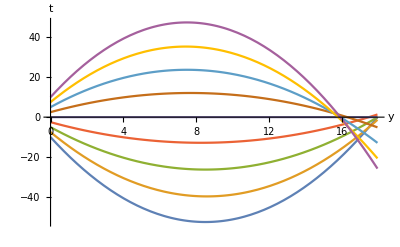

```mathematica
(*Trajektorie*)
ysToPlot=Table[y,{y,-ymax,ymax,2.5}];
Plot[Evaluate@Table[xi[y,t],{y,-ymax,ymax,2.5}],{t,0,tmax},AxesLabel->{"y","t"}]
```

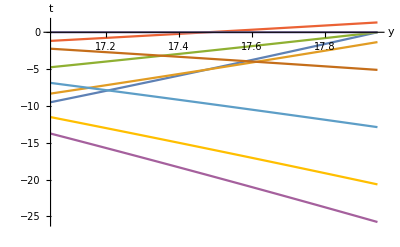

```mathematica
Plot[Evaluate@Table[xi[y,t],{y,-ymax,ymax,2.5}],{t,tmax*.95,tmax},AxesLabel->{"y","t"}]
```

```mathematica
(*wykres przeskalowanej gęstości: rho[x/a[t],t] dla rho[y]=rho0 *)
rhotxScaled[x_,t_]:=(rho0y[(x/a[t])]Abs[xiDy[(x/a[t]) ,t]]^(-1))
Plot3D[rhotxScaled[x,t],{x,-ymax*amax,ymax*amax},{t,0,tmax},AxesLabel->{"x","t"}]
```

-Graphics3D-

```mathematica
(*Wykres przeskalowanej gęstości pędu [x/a[t]]*)
Plot3D[momentumDensityScaled[x,t],{x,-ymax*amax,ymax*amax},{t,0,tmax},AxesLabel->{"x","t"}]
```

-Graphics3D-

```mathematica
tMerge[y]:=(
(H + Sqrt[H^2+4 Pi G rho0y[y]])/(4 Pi G rho0y[y])
)
```

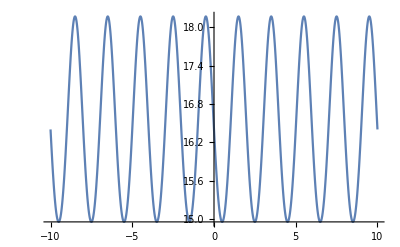

```mathematica
Plot[tMerge[y],{y,-ymax,ymax}]
```

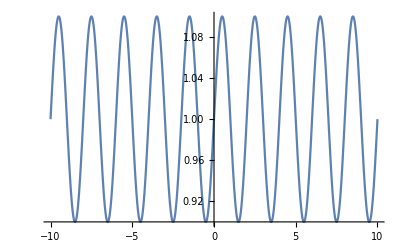

```mathematica
Plot[rho0y[y],{y,-ymax,ymax}]
```

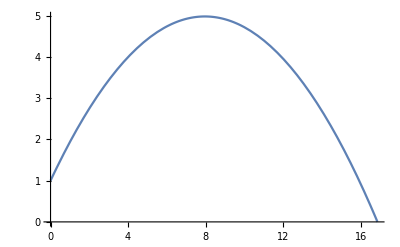

```mathematica
Plot[a[t],{t,0,tmax}]
```

```mathematica
tmax
```

16.8595